## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetOptions[EvaluationNotebook[],CellContext -> Notebook]
SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TRPS1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3_milos_assume_Km_desktop_adjusted_KEQS.csv";

mainFolder = "fit_TRPS1_Final_Assumed_Km_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

((3ig3p)^c+ser__L^c⇌g3p^c+trp__L^c)^TRPS1

bi-bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p | Null | 135032. | 128280.
141783. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ser__L | 0.0001 | 0.000095
0.000105 |  | M | 7.5 | 37 |  | 
1 | 3ig3p | 0.000041 | 0.00003895
0.00004305 |  | M | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p | Null | 6.64 | 6.308
6.972 | 1/s | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {10};(*Note: we use only one set of Km's and kcat's here because the paper has a combined alpha and beta subunit value and a individual subunit value*)
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3ig3p)^c+ser__L^c⇌g3p^c+trp__L^c)^TRPS1

bi-bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | 3ig3p | Null | 135032. | 128280.
141783. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ser__L | 0.0001 | 0.000095
0.000105 |  | M | 7.5 | 37 |  | 
1 | 3ig3p | 0.000041 | 0.00003895
0.00004305 |  | M | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | 3ig3p | Null | 6.64 | 6.308
6.972 | 1/s | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TRPS1[c] + 3ig3p[c] <=> E_TRPS1[c]&3ig3p",
				"E_TRPS1[c]&3ig3p <=> E_TRPS1[c]&indole&g3p",
				"E_TRPS1[c]&indole&g3p <=> E_TRPS1[c]&indole + g3p[c]",
				"E_TRPS1[c]&indole + ser__L[c] <=> E_TRPS1[c]&indole&ser__L",
				"E_TRPS1[c]&indole&ser__L <=> E_TRPS1[c]&trp__L",
				"E_TRPS1[c]&trp__L <=> E_TRPS1[c] + trp__L[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TRPS1^c)_^+(3ig3p)^c⇌(TRPS1^c&(3ig3p)^c)_^)^TRPS11,((TRPS1^c&trp_^L)_^⇌(TRPS1^c)_^+trp__L^c)^TRPS12,((TRPS1^c&indole^c)_^+ser__L^c⇌(TRPS1^c&indole^c&ser_^L)_^)^TRPS13,((TRPS1^c&(3ig3p)^c)_^⇌(TRPS1^c&indole^c&g3p^c)_^)^TRPS14,((TRPS1^c&indole^c&ser_^L)_^⇌(TRPS1^c&trp_^L)_^)^TRPS15,((TRPS1^c&indole^c&g3p^c)_^⇌(TRPS1^c&indole^c)_^+g3p^c)^TRPS16}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TRPS1^c)_^+(3ig3p)^c⇌(TRPS1^c&(3ig3p)^c)_^)^TRPS11,Overscript[(TRPS1^c&trp_^L)_^⇌(TRPS1^c)_^+trp__L^c, TRPS12],((TRPS1^c&indole^c)_^+ser__L^c⇌(TRPS1^c&indole^c&ser_^L)_^)^TRPS13,((TRPS1^c&(3ig3p)^c)_^⇌(TRPS1^c&indole^c&g3p^c)_^)^TRPS14,((TRPS1^c&indole^c&ser_^L)_^⇌(TRPS1^c&trp_^L)_^)^TRPS15,Overscript[(TRPS1^c&indole^c&g3p^c)_^⇌(TRPS1^c&indole^c)_^+g3p^c, TRPS16]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2; (*Combined complex has 4 active sites, but only two of each type. Since both active sites are used in this mechanism, I'm listing two*)
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((TRPS1^c&(3ig3p)^c)_^-((TRPS1^c&indole^c&g3p^c)_^)/K_TRPS14) Volume_c k_TRPS14^⟶,((TRPS1^c&indole^c&ser_^L)_^-((TRPS1^c&trp_^L)_^)/K_TRPS15) Volume_c k_TRPS15^⟶}

Volume_c (-(TRPS1^c&indole^c&g3p^c)_^ k_TRPS14^⟵+(TRPS1^c&(3ig3p)^c)_^ k_TRPS14^⟶-(TRPS1^c&trp_^L)_^ k_TRPS15^⟵+(TRPS1^c&indole^c&ser_^L)_^ k_TRPS15^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur = 135032;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_TRPS11^⟵

k_TRPS11^⟵→(k_TRPS11^⟶ k_TRPS12^⟶ k_TRPS13^⟶ k_TRPS14^⟶ k_TRPS15^⟶ k_TRPS16^⟶)/(135032 k_TRPS12^⟵ k_TRPS13^⟵ k_TRPS14^⟵ k_TRPS15^⟵ k_TRPS16^⟵)

```mathematica
flux = 0.00002579694921354;(*added in a much higher flux to compensate for lack of products*)
FluxExpression = absoluteFlux /. {metabolite["3ig3p", "c"] -> 0.0000001826867,metabolite["ser__L","c"]-> 0.000055673691209,
metabolite["trp__L","c"]-> 0.000009907,metabolite["g3p","c"]-> 0.00001539,
     parameter["TRPS1_total"] -> 0.0000104076, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "TRPS1"] /. FluxExpression/.haldaneSub[[1,1]];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{10,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
Print[metSatRevSub]
```

{g3p^c→1,trp__L^c→1}

```mathematica
FilePrint@dataPathList
```

Priority	3ig3p[c]	g3p[c]	ser__L[c]	trp__L[c]	param_TRPS1_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt"	135031.8001
1	1	0	0.00001	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.09090909090909091
1	1	0	0.00001584893192461114	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.13680688860321005
1	1	0	0.000025118864315095822	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.20076000891310186
1	1	0	0.000039810717055349695	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.2847472489508013
1	1	0	0.00006309573444801929	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.3868631798468568
1	1	0	0.0001	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.5
1	1	0	0.00015848931924611142	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.6131368201531432
1	1	0	0.0002511886431509582	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.7152527510491988
1	1	0	0.00039810717055349735	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.7992399910868982
1	1	0	0.000630957344480193	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.8631931113967899
1	1	0	0.001	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt"	0.9090909090909091
1	4.1e-6	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.0909090909090909
1	6.498062089090567e-6	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.13680688860321003
1	0.000010298734369189286	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.20076000891310186
1	0.000016322393992693374	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.2847472489508012
1	0.00002586925112368791	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.38686317984685686
1	0.000040999999999999994	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.5
1	0.00006498062089090567	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.6131368201531431
1	0.00010298734369189285	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.7152527510491987
1	0.00016322393992693388	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.7992399910868982
1	0.0002586925112368791	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.8631931113967899
1	0.00040999999999999994	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt"	0.9090909090909091
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	1	0	1	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt"	6.64
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt"	0.00002579694921354

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {allFittingDataList,dataPathList,fileList,fileListSub} and … are not the same shape.

```mathematica
FilePrint[dataPathList[[1]]]
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦1⟧ is longer than depth of object.

FilePrint::badfile: The specified argument /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦1⟧ should be a valid string or File.

FilePrint[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦1⟧]

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {allFittingDataList,dataPathList,fileList,fileListSub} and … are not the same shape.

```mathematica
FilePrint[dataPathList[[18]]]
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦18⟧ is longer than depth of object.

FilePrint::badfile: The specified argument /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦18⟧ should be a valid string or File.

FilePrint[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦18⟧]

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateRev_trp__L.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateFor_ser__L.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/relRateRev_trp__L.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS1_Final_Assumed_Km_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 3.27532479242
best_fit: 4.85735273966
best_fit: 3.24901652106
best_fit: 3.06103968402
best_fit: 3.02416551517
best_fit: 5.80341518878
best_fit: 5.8433650801
best_fit: 5.36541124718
best_fit: 2.97330343027
best_fit: 2.99294833671

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/New_Rate_Constss/PGL/fit_TRPS1_Final_Assumed_Km_typeII/input/TRPS1_TRPS1.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
10 | haldaneRatio_1 | 1.56328×10^-6 | 2.44384×10^-12 | 0.486059 | 0.000359959 | 135032. | 135032.
1 | relRateFor_ser__L | 0.0364901 | 0.00133153 | 0.0079684 | 8.76524 | 0.0909091 | 0.0988775
1 | relRateFor_ser__L | 0.0345746 | 0.0011954 | 0.0113366 | 8.28657 | 0.136807 | 0.148143
1 | relRateFor_ser__L | 0.0319196 | 0.00101886 | 0.0153111 | 7.62659 | 0.20076 | 0.216071
1 | relRateFor_ser__L | 0.0284573 | 0.000809819 | 0.019283 | 6.77199 | 0.284747 | 0.30403
1 | relRateFor_ser__L | 0.0242846 | 0.000589741 | 0.0222486 | 5.75102 | 0.386863 | 0.409112
1 | relRateFor_ser__L | 0.0197078 | 0.000388399 | 0.0232122 | 4.64243 | 0.5 | 0.523212
1 | relRateFor_ser__L | 0.0151788 | 0.000230396 | 0.0218083 | 3.55684 | 0.613137 | 0.634945
1 | relRateFor_ser__L | 0.0111311 | 0.000123902 | 0.0185691 | 2.59617 | 0.715253 | 0.733822
1 | relRateFor_ser__L | 0.00783008 | 0.0000613102 | 0.0145405 | 1.81929 | 0.79924 | 0.813781
1 | relRateFor_ser__L | 0.00533318 | 0.0000284428 | 0.0106654 | 1.23558 | 0.863193 | 0.873859
1 | relRateFor_ser__L | 0.00355001 | 0.0000126026 | 0.00746154 | 0.82077 | 0.909091 | 0.916552
1 | relRateFor_3ig3p | 1.04067 | 1.083 | 0.907435 | 998.178 | 0.0909091 | 0.998344
1 | relRateFor_3ig3p | 0.863438 | 0.745525 | 0.862148 | 630.193 | 0.136807 | 0.998955
1 | relRateFor_3ig3p | 0.697036 | 0.485859 | 0.79858 | 397.778 | 0.20076 | 0.99934
1 | relRateFor_3ig3p | 0.54536 | 0.297417 | 0.714836 | 251.042 | 0.284747 | 0.999584
1 | relRateFor_3ig3p | 0.412328 | 0.170015 | 0.612874 | 158.421 | 0.386863 | 0.999737
1 | relRateFor_3ig3p | 0.300958 | 0.0905757 | 0.499834 | 99.9668 | 0.5 | 0.999834
1 | relRateFor_3ig3p | 0.212397 | 0.0451126 | 0.386759 | 63.0787 | 0.613137 | 0.999895
1 | relRateFor_3ig3p | 0.145512 | 0.0211737 | 0.284681 | 39.8015 | 0.715253 | 0.999934
1 | relRateFor_3ig3p | 0.0973047 | 0.00946821 | 0.200718 | 25.1137 | 0.79924 | 0.999958
1 | relRateFor_3ig3p | 0.0638806 | 0.00408073 | 0.136781 | 15.8459 | 0.863193 | 0.999974
1 | relRateFor_3ig3p | 0.0413855 | 0.00171276 | 0.0908925 | 9.99818 | 0.909091 | 0.999983
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | absRateFor | 0.0002111 | 4.4563×10^-8 | 0.00322832 | 0.0486193 | 6.64 | 6.64323
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834
10 | customRatio_1 | 0.000228991 | 5.2437×10^-8 | 1.35984×10^-8 | 0.0527133 | 0.0000257969 | 0.0000257834

### Simulated Data and Best Fit Data Plot

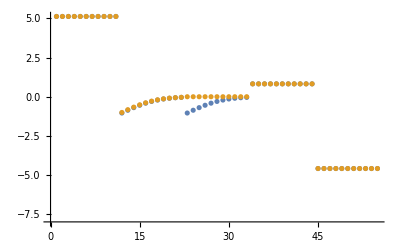

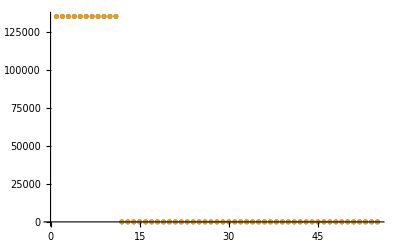

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

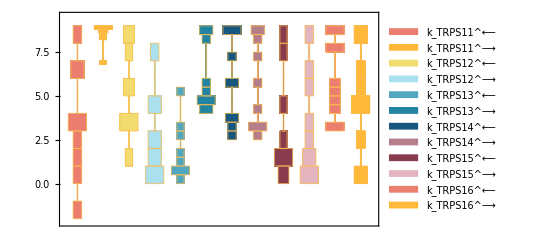

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

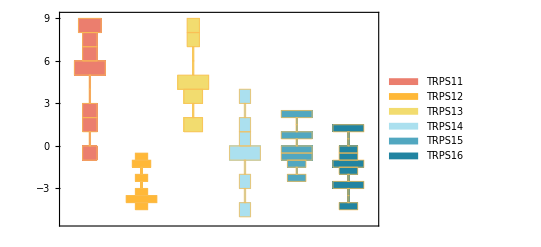

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24]
(*Histogram*)
```

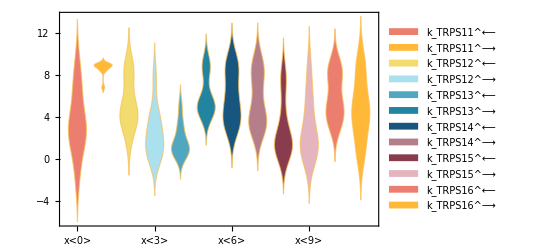

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

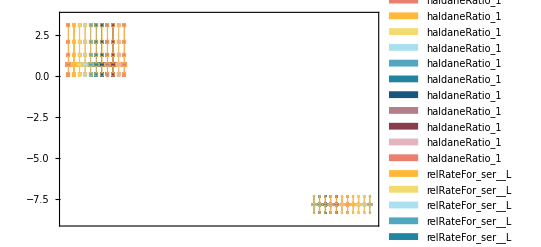

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0001 | 0.0000911279 | 8.87214
0.000041 | 6.80075×10^-9 | 99.9834

```mathematica
assumedSaturatingConc
```

1

```mathematica
Print[absoluteRateForward]
```

(4 (3ig3p)^c ser__L^c TRPS1_total_Global k_TRPS11^⟶ k_TRPS12^⟶ k_TRPS13^⟶ k_TRPS14^⟶ k_TRPS15^⟶ k_TRPS16^⟶)/((3ig3p)^c k_TRPS11^⟶ k_TRPS14^⟶ (k_TRPS13^⟵ k_TRPS15^⟵+k_TRPS12^⟶ (k_TRPS13^⟵+k_TRPS15^⟶)) k_TRPS16^⟶+ser__L^c k_TRPS13^⟶ (k_TRPS12^⟶ k_TRPS14^⟶ k_TRPS15^⟶ k_TRPS16^⟶+k_TRPS11^⟵ k_TRPS12^⟶ k_TRPS15^⟶ (k_TRPS14^⟵+k_TRPS16^⟶)+(3ig3p)^c k_TRPS11^⟶ (k_TRPS14^⟶ (k_TRPS15^⟵+k_TRPS15^⟶) k_TRPS16^⟶+k_TRPS12^⟶ (k_TRPS14^⟵ k_TRPS15^⟶+k_TRPS15^⟶ k_TRPS16^⟶+k_TRPS14^⟶ (k_TRPS15^⟶+k_TRPS16^⟶)))))

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
6.64 | 0. | 100.

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
135032. | 135032. | 0.000359959

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
135032. | 135032. | 0.000359959

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm 
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

data value | predicted value | error in %

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

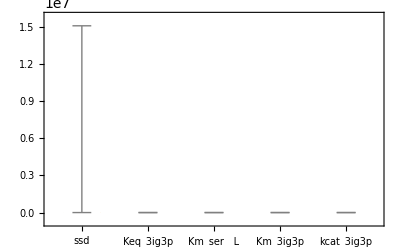

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/trps1 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\rateconst_labels_trps1.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\S_trps1.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_TRPS1[c],E_TRPS1[c]&3ig3p,E_TRPS1[c]&indole,E_TRPS1[c]&trp_[L],E_TRPS1[c]&indole&g3p,3ig3p[c],g3p[c],ser__L[c],trp__L[c],E_TRPS1[c]&indole&ser_[L]}

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\species_trps1.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{TRPS11: 3ig3p[c] + E_TRPS1[c] <=> E_TRPS1[c]&3ig3p,TRPS12: E_TRPS1[c]&trp_[L] <=> E_TRPS1[c] + trp__L[c],TRPS13: E_TRPS1[c]&indole + ser__L[c] <=> E_TRPS1[c]&indole&ser_[L],TRPS14: E_TRPS1[c]&3ig3p <=> E_TRPS1[c]&indole&g3p,TRPS15: E_TRPS1[c]&indole&ser_[L] <=> E_TRPS1[c]&trp_[L],TRPS16: E_TRPS1[c]&indole&g3p <=> E_TRPS1[c]&indole + g3p[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\reactions_trps1.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/New_Rate_Constss/PGL/fit_TRPS1_Final_Assumed_Km_typeII/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_TRPS1[c],E_TRPS1[c]&3ig3p,E_TRPS1[c]&indole,E_TRPS1[c]&trp_[L],E_TRPS1[c]&indole&g3p,E_TRPS1[c]&indole&ser_[L]}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(g3p(c)*k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_rev*k_TRPS14_rev*k_TRPS16_rev*param_TRPS1_total) - g3p(c)*k_TRPS11_rev*k_TRPS12_fwd*k_TRPS14_rev*k_TRPS15_fwd*k_TRPS16_rev*param_TRPS1_total - g3p(c)*k_TRPS11_rev*k_TRPS13_rev*k_TRPS14_rev*k_TRPS15_rev*k_TRPS16_rev*param_TRPS1_total - k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_rev*k_TRPS15_fwd*param_TRPS1_total*ser__L(c) - k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS15_fwd*k_TRPS16_fwd*param_TRPS1_total*ser__L(c) - k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_fwd*param_TRPS1_total*ser__L(c))/(3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS16_fwd + 3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_fwd + 3ig3p(c)*k_TRPS11_fwd*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_fwd + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS16_rev + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_rev*k_TRPS14_rev*k_TRPS16_rev + g3p(c)*k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_rev*k_TRPS14_rev*k_TRPS16_rev + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_rev + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS14_rev*k_TRPS15_fwd*k_TRPS16_rev + g3p(c)*k_TRPS11_rev*k_TRPS12_fwd*k_TRPS14_rev*k_TRPS15_fwd*k_TRPS16_rev + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_rev + 3ig3p(c)*g3p(c)*k_TRPS11_fwd*k_TRPS13_rev*k_TRPS14_rev*k_TRPS15_rev*k_TRPS16_rev + g3p(c)*k_TRPS11_rev*k_TRPS13_rev*k_TRPS14_rev*k_TRPS15_rev*k_TRPS16_rev + 3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_fwd*ser__L(c) + 3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_rev*k_TRPS15_fwd*ser__L(c) + k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_rev*k_TRPS15_fwd*ser__L(c) + 3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS16_fwd*ser__L(c) + 3ig3p(c)*k_TRPS11_fwd*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c) + k_TRPS11_rev*k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c) + 3ig3p(c)*k_TRPS11_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c) + k_TRPS12_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c) + 3ig3p(c)*k_TRPS11_fwd*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_fwd*ser__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_rev*k_TRPS14_rev*k_TRPS15_rev*trp__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_rev*k_TRPS15_rev*k_TRPS16_fwd*trp__L(c) + k_TRPS12_rev*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_fwd*trp__L(c) + g3p(c)*k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_rev*k_TRPS14_rev*k_TRPS16_rev*trp__L(c) + g3p(c)*k_TRPS11_rev*k_TRPS12_rev*k_TRPS14_rev*k_TRPS15_fwd*k_TRPS16_rev*trp__L(c) + g3p(c)*k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_rev*k_TRPS15_rev*k_TRPS16_rev*trp__L(c) + g3p(c)*k_TRPS12_rev*k_TRPS13_rev*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_rev*trp__L(c) + g3p(c)*k_TRPS11_rev*k_TRPS12_rev*k_TRPS14_rev*k_TRPS15_rev*k_TRPS16_rev*trp__L(c) + g3p(c)*k_TRPS12_rev*k_TRPS13_rev*k_TRPS14_rev*k_TRPS15_rev*k_TRPS16_rev*trp__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_fwd*k_TRPS14_rev*k_TRPS15_fwd*ser__L(c)*trp__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_fwd*k_TRPS14_rev*k_TRPS15_rev*ser__L(c)*trp__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c)*trp__L(c) + k_TRPS12_rev*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_fwd*k_TRPS16_fwd*ser__L(c)*trp__L(c) + k_TRPS11_rev*k_TRPS12_rev*k_TRPS13_fwd*k_TRPS15_rev*k_TRPS16_fwd*ser__L(c)*trp__L(c) + k_TRPS12_rev*k_TRPS13_fwd*k_TRPS14_fwd*k_TRPS15_rev*k_TRPS16_fwd*ser__L(c)*trp__L(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\rateconst_clusters_trps1.txt

```mathematica
solRateEq = Import["//Users/guest/Desktop/internship stuff/MASSef/examples/New_Rate_Constss/PGL/fit_TRPS1_Final_Assumed_Km_typeII/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/trps1\rateLaw_trps1.txt